```mathematica
BisectionMWE[a0_,b0_,n_,f_]:=
Module[{},a=N[a0];b=N[b0];m=(a+b)/2;
i=0;If[f[a]*f[b]>0,Print["We cannot continue with the Bisection Method"];Return[]];
Output={{i,a,m,b,f[m]}};
While[i<n,If[Sign[f[a]]==Sign[f[m]],a=m,b=m];
m=(a+b)/2;i++;
Output=Append[Output,{i,a,m,b,f[m]}];];
Print[NumberForm[TableForm[Output,TableHeadings->{None,{"i","ai","mi","bi","f[mi]"}}],8]];
Print["Root after ",n," iterations = ",NumberForm[m,8]];
Print["Accuracy = ",Abs[(b-a)/2]];
Print["Function value at approximated root, f[m]= ",NumberForm[f[m],8]];];
```

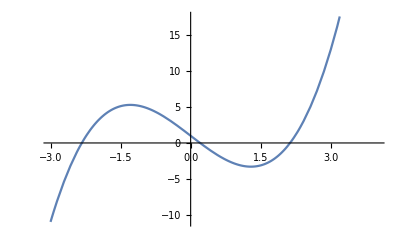

```mathematica
f[x_]:=x^3-5x+1;
Plot[f[x],{x,-3,4}]
```

```mathematica
BisectionMWE[3,4,10,f]
```

We cannot continue with the Bisection Method

```mathematica
BisectionMWE[0,1,10,f]
```

i | ai | mi | bi | f[mi]
0 | 0. | 0.5 | 1. | -1.375
1 | 0. | 0.25 | 0.5 | -0.234375
2 | 0. | 0.125 | 0.25 | 0.37695313
3 | 0.125 | 0.1875 | 0.25 | 0.069091797
4 | 0.1875 | 0.21875 | 0.25 | -0.083282471
5 | 0.1875 | 0.203125 | 0.21875 | -0.0072441101
6 | 0.1875 | 0.1953125 | 0.203125 | 0.030888081
7 | 0.1953125 | 0.19921875 | 0.203125 | 0.011812866
8 | 0.19921875 | 0.20117188 | 0.203125 | 0.0022820756
9 | 0.20117188 | 0.20214844 | 0.203125 | -0.0024815956
10 | 0.20117188 | 0.20166016 | 0.20214844 | -0.000099904253

Root after 10 iterations = 0.20166016

Accuracy = 0.000488281

Function value at approximated root, f[m]= -0.000099904253

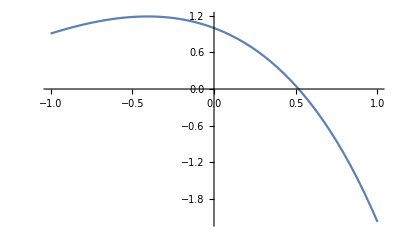

```mathematica
f[x_]:=Cos[x]-x Exp[x]
Plot[f[x],{x,-1,1}]
```

```mathematica
BisectionMWE[0,1,10,f]
```

i | ai | mi | bi | f[mi]
0 | 0. | 0.5 | 1. | 0.053221927
1 | 0.5 | 0.75 | 1. | -0.85606114
2 | 0.5 | 0.625 | 0.75 | -0.3566906
3 | 0.5 | 0.5625 | 0.625 | -0.14129375
4 | 0.5 | 0.53125 | 0.5625 | -0.041512212
5 | 0.5 | 0.515625 | 0.53125 | 0.0064753408
6 | 0.515625 | 0.5234375 | 0.53125 | -0.017362025
7 | 0.515625 | 0.51953125 | 0.5234375 | -0.0054044018
8 | 0.515625 | 0.51757813 | 0.51953125 | 0.00054518442
9 | 0.51757813 | 0.51855469 | 0.51953125 | -0.0024271775
10 | 0.51757813 | 0.51806641 | 0.51855469 | -0.00094038902

Root after 10 iterations = 0.51806641

Accuracy = 0.000488281

Function value at approximated root, f[m]= -0.00094038902

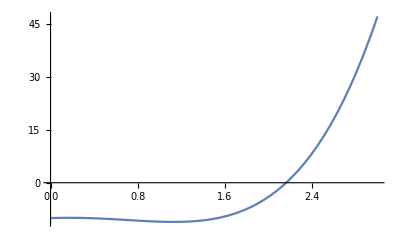

```mathematica
f[x_]=x^4-3x^2+x-10;
Plot[f[x],{x,0,3}]
```

```mathematica
BisectionMWE[2,3,12,f]
```

i | ai | mi | bi | f[mi]
0 | 2. | 2.5 | 3. | 12.8125
1 | 2. | 2.25 | 2.5 | 2.6914063
2 | 2. | 2.125 | 2.25 | -1.0310059
3 | 2.125 | 2.1875 | 2.25 | 0.72975159
4 | 2.125 | 2.15625 | 2.1875 | -0.17494106
5 | 2.15625 | 2.171875 | 2.1875 | 0.2712279
6 | 2.15625 | 2.1640625 | 2.171875 | 0.046611492
7 | 2.15625 | 2.1601563 | 2.1640625 | -0.06454622
8 | 2.1601563 | 2.1621094 | 2.1640625 | -0.0090629158
9 | 2.1621094 | 2.1630859 | 2.1640625 | 0.018750376
10 | 2.1621094 | 2.1625977 | 2.1630859 | 0.004837755
11 | 2.1621094 | 2.1623535 | 2.1625977 | -0.0021140738
12 | 2.1623535 | 2.1624756 | 2.1625977 | 0.0013614672

Root after 12 iterations = 2.1624756

Accuracy = 0.00012207

Function value at approximated root, f[m]= 0.0013614672